# Trust Region Approximations

Our book discusses various approximate solutions for the standard trust region problem
	p^*=argmin_(||p||≤Δ)0.5p.B.p+g.p
we want to compare these to the GEV algorithm.  The overall aim is to get a decent approximation reasonably cheaply.  All of them will check for a feasible internal min. The directions that are available are -g the steepest descent direction and -B^-1g the Newton step.

## Algorithm Overview: Cheap to Less Cheap

The simplest step is “steepest descent” but in the trust region language it is the Cauchy point
	p_C=-g/(||g||)Δ

Our book next discusses dogleg steps. Dogleg steps leave the origin in the steepest descent direction if they hit a minimum before they hit the boundary they turn and head to the Newton point p_N=-A^-1g.  They stop when they hit the boundary.

Two D minimization scheme computes an accurate solution (satisfying the constraint) over the 2D span 
	sp{p_C,p_N}.
This algorithm is a 2D version of the GEV algorithm!

Section 4.3 discusses a more ambitious approximation technique. First note that 
	p(λ)= -(B+λ I)^-1.g with ||p(λ)||=Δ
for some λ>0 with B+λ I≻0 unless there is an internal critical point.

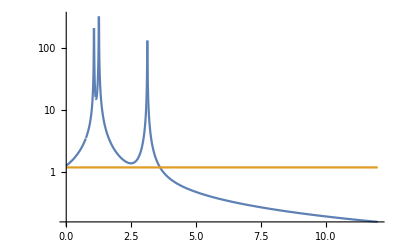

```mathematica
n=7;
B=RandomReal[{-1,1},{n,n}]; B = B + Bᵀ;
g=RandomReal[{-1,1},n];
Δ=1.2;
LogPlot[ {Norm[ LinearSolve[B+ λ IdentityMatrix[n],-g]],Δ},{λ,0, 12},PlotRange->All]
```

## More and Sorensen

Details from 
Copy in References
@article{Mor1983ComputingAT,
  title={Computing a Trust Region Step},
  author={Jorge J. Mor{\’e} and Danny C. Sorensen},
  journal={Siam Journal on Scientific and Statistical Computing},
  year={1983},
  volume={4},
  pages={553-572}
}

Found a more recent matlab implementation specialized to LBFGS
Algorithm 943
Jennifer B. Erway, R. Marcia
Computer Science
2014

TLDR
A MATLAB implementation of the Moré-Sorensen sequential (MSS) method that computes the minimizer of a quadratic function defined by a limited-memory BFGS matrix subject to a two-norm trust-region constraint is presented.
Abstract
A MATLAB implementation of the Moré-Sorensen sequential (MSS) method is presented. The MSS method computes the minimizer of a quadratic function defined by a limited-memory BFGS matrix subject to a two-norm trust-region constraint. This solver is an adaptation of the Moré-Sorensen direct method into an L-BFGS setting for large-scale optimization. The MSS method makes use of a recently proposed stable fast direct method for solving large shifted BFGS systems of equations [Erway and Marcia 2012; Erway et al. 2012] and is able to compute solutions to any user-defined accuracy. This MATLAB implementation is a matrix-free iterative method for large-scale optimization. Numerical experiments on the CUTEr [Bongartz et al. 1995; Gould et al. 2003]) suggest that using the MSS method as a trust-region subproblem solver can require significantly fewer function and gradient evaluations needed by a trust-region method as compared with the Steihaug-Toint method.

Back to the original M&S paper.  A Fortran code called GQTPAR is referenced.  I found a C version  on github at
	https://github.com/emmt/OptimPack/blob/master/src/gqtpar.c
I could translate this.  Last update was April 2022.

Here is Algorithm 3.2 p556.  Assumption is that λ>0 and B+λ I is SPD and Δ>0

```mathematica
MSAlg3Point2[B_,g_,Δ_,λ_]:= Module[{n=Length[B],R,p,q},
(* Assumption is that λ>0 andB+λ I is SPD and Δ>0 *)
(* Not worried about efficiency right now *)
R=CholeskyDecomposition[B+λ IdentityMatrix[n]];
p=LinearSolve[B+λ IdentityMatrix[n],-g];
q=LinearSolve[Rᵀ,p];
λ+(Norm[p]/Norm[q])^2((Norm[p]-Δ)/Δ)
]
```

```mathematica
n=4;
A=RandomReal[{-1,1},{n,n}];A=A+Aᵀ;
Min[Eigenvalues[A]]
```

-1.7176